```mathematica
Quit[];
```

# Electroweak baryogenesis at high wall velocities (arXiv:2001.00568)

## Master Code Reformulated

```mathematica
ClearAll["Global`*"];
(*SetDirectory[NotebookDirectory[]];*)
```

```mathematica
SetOptions[{ParametricPlot,ListLinePlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot,ListContourPlot,LogPlot,Plot,RegionPlot,ContourPlot},Frame->True,BaseStyle->{FontColor->Black,FontWeight->"Normal",FontSize->16,FontFamily->"Times"},Axes->False,PlotLegends->Automatic,AspectRatio->1,ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->Full];
colours=ColorData[97,"ColorList"];
```

```mathematica
WP=MachinePrecision;
(*******************************************************************************************************************)
(**********************************************************************************************)
```

```mathematica
(*gtab=Import["standardmodel2018.txt","Table",HeaderLines->8][[;;;;20]];*)
gtab=Import["/Users/marcoantoniomerchandmedina/Documents/GitHub/Z_2breaking/satoshi_dof.dat","Table",HeaderLines->8][[;;;;20]];
gstar[T_]:=Interpolation[gtab[[All,{1,2}]]][T];
gsstar[T_]:=Interpolation[gtab[[All,{1,4}]]][T];
(*****************************************************************************************************)
(*****************************************************************************************************)
```

```mathematica
(*params3=Import["SCANS/BAU/Z2_breaking_sols_BAU_All.csv","Dataset","HeaderLines"->1];
Tnlist=params3[All,"Tnuc_0"];
TpoverTnlist=params3[All,"Tp/TN"];
vwlist=params3[All,"vw"];
vplist=params3[All,"vp"];
h0list=params3[All,"h0"];
Lhlist=params3[All,"Lh"];
Lslist=params3[All,"Ls"];
dslist=params3[All,"ds"];
shighlist=params3[All,"shigh"];
slowlist=params3[All,"slow"];
alphalist=params3[All,"alpha_max"];*)
```

```mathematica
params3=Import["/Users/marcoantoniomerchandmedina/Documents/GitHub/Z_2breaking/SCANS/computeBAU.csv","Dataset","HeaderLines"->1];
Tnlist=params3[All,"Tnuc_0"]//Normal;
TpoverTnlist=params3[All,"Tp/TN"]//Normal;
vwlist=params3[All,"vw"]//Normal;
vplist=params3[All,"vp"]//Normal;
h0list=params3[All,"h0"]//Normal;
Lhlist=params3[All,"Lh"]//Normal;
Lslist=params3[All,"Ls"]//Normal;
dslist=params3[All,"ds"]//Normal;
shighlist=params3[All,"shigh"]//Normal;
slowlist=params3[All,"slow"]//Normal;
alphalist=params3[All,"alpha_max"]//Normal;
mslist=params3[All,"ms"]//Normal;Lamlist=params3[All,"Lam_CP"]//Normal;
```

```mathematica
MasterFunction[Tn_,vw_,h0_,Lh_,sl_,sh_,Ls_,ds_,ΛCP_,Infty_,points_]:=MasterFunction[Tn,vw,h0,Lh,sl,sh,Ls,ds,ΛCP,Infty,points]=Module[{ηobs=8 10^-11,β=1/Tn,Γsph=10^-6 Tn,h,s,mt,Bond,Equation,sol,μtlsol,μtrsol,μblsol,μhsol,μBL,fsph,gdof,ηB,Plot1,Plot2,
ΓSS=4.9*10^-4 Tn,
Γy=4.2*10^-3 Tn,Dq=6/Tn(*quark diffusion constant*),
Dh=20/Tn(*higgs diffusion constant*),
inf=Infty Lh (*defines the region of interpolation/integration*)},
pw=√(w^2-x^2);(*Formula defined after A3*)
pz=1/(√(1-vw^2))(y pw-w vw);(*Formula defined after A3*)
Eb=1/(√(1-vw^2))(w-vw y pw);(*Formula defined after A3*)
Vs = √(pz^2)/√(pz^2+x^2);(*Formula  A4*)
Vh=Vs^2 1/(√(1-x^2/Eb^2));(*Formula  A5*);
ff=1/(Exp[β w]+1);(*Distribution funcion for fermion *)
fb=1/(Exp[β w]-1);(*Distribution funcion for boson *)
ff1=D[ff,w];(*Derivative of Distribution funcion for fermion *)
fb1=D[fb,w];(*Derivative of Distribution funcion for boson *)
ff2=D[ff1,w];(*Second Derivative of Distribution funcion for fermion *)
fb2=D[fb1,w];(*Second Derivative of Distribution funcion for boson *)
h[z_]:=h0/2(Tanh[z/Lh]+1);(**equation (50) LEFT MOVING WALL!!**)
(*s[z_]:=s0/2(1-Tanh[z/Ls-ds]);*)(**equation (50)**)
s[z_]:=(sl-sh)/2 Tanh[z/Ls-ds]+(sl+sh)/2;
mt[z_]:=0.99571/(√2) h[z] √(1+s[z]^2/ΛCP^2);(**equation (49)**)
θ[z_]:=ArcTan[s[z]/ΛCP];(**equation (49)**)
mb[z_]:=4.2*h[z]/h0 ;
mh[z_]:=125.3*h[z]/h0 ;
Γm[z_]:=mt[z]^2/(63 Tn);
mW[z_]:=0.65 h[z]/2 (*W boson mass*);
Γh[z_]:=mW[z]^2/(50Tn);
Xmax=Max[{mt[inf],mh[inf],mb[inf],mW[inf]}]+0.1(*Max value of x used for interpolating coefficient functions*);Kf0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2 NIntegrate[pw Eb ff/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for fermions*);
Kb0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for bosons*);
Kf0inter=Interpolation[Table[{x,Kf0[x,vw]},{x,0,Xmax,Xmax/10}]];
Kb0inter=Interpolation[Table[{x,Kb0[x,vw]},{x,0,Xmax,Xmax/10}]];
K0t[z_]:=Kf0inter[mt[z]];
K0b[z_]:=Kf0inter[mb[z]];
K0h[z_]:=Kb0inter[mh[z]];Df0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=0*);
Db0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=0*);Df0inter=Interpolation[Table[{x,Df0[x,vw]},{x,0,Xmax,Xmax/10}]];
Db0inter=Interpolation[Table[{x,Db0[x,vw]},{x,0,Xmax,Xmax/10}]];
D0t[z_]:=Df0inter[mt[z]];
D0b[z_]:=Df0inter[mb[z]];
D0h[z_]:=Db0inter[mh[z]];Df1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=1*);
Db1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=1*);
Df1inter=Interpolation[Table[{x,Df1[x,vw]},{x,0,Xmax,Xmax/10}]];
Db1inter=Interpolation[Table[{x,Db1[x,vw]},{x,0,Xmax,Xmax/10}]];
D1t[z_]:=Df1inter[mt[z]];
D1b[z_]:=Df1inter[mb[z]];
D1h[z_]:=Db1inter[mh[z]];Df2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=2*);
Db2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=2*);Df2inter=Interpolation[Table[{x,Df2[x,vw]},{x,0,Xmax,Xmax/10}]];
Db2inter=Interpolation[Table[{x,Db2[x,vw]},{x,0,Xmax,Xmax/10}]];
D2t[z_]:=Df2inter[mt[z]];
D2b[z_]:=Df2inter[mb[z]];
D2h[z_]:=Db2inter[mh[z]];Qf1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[pw  ff2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞}](*Formula (27) for fermions, l=1*);
Qb1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[pw  fb2/.{x->0,vvw->vi},{y,-1,1}],{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw  fb2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞},WorkingPrecision->10]](*Formula (27) for bosons, l=1*);
Qf1inter=Interpolation[Table[{x,Qf1[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb1inter=Interpolation[Table[{x,Qb1[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1t[z_]:=Qf1inter[mt[z]];
Q1b[z_]:=Qf1inter[mb[z]];
Q1h[z_]:=Qb1inter[mh[z]];
Qf2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[(pw pz)/Eb ff2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10](*Formula (27) for fermions, l=2*);
Qb2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{y,-1,1}],{w,xi,∞,xi},Method->PrincipalValue],NIntegrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (27) for bosons, l=2*);Qf2inter=Interpolation[Table[{x,Qf2[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb2inter=Interpolation[Table[{x,Qb2[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2t[z_]:=Qf2inter[mt[z]];
Q2b[z_]:=Qf2inter[mb[z]];
Q2h[z_]:=Qb2inter[mh[z]];
Q1fo8integrand=FullSimplify[(Integrate[pw/pz Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh ff1/.{x->0,vw->vi},y]/.{y->-1})];Q1bo8integrand=FullSimplify[(Integrate[pw/pz Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh fb1/.{x->0,vw->vi},y]/.{y->-1})];Q1fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=1, helicity eigenstates*);
Q1bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=1, helicity eigenstates*);Q1fo8inter=Interpolation[Table[{x,Q1fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1bo8inter=Interpolation[Table[{x,Q1bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o8t[z_]:=Q1fo8inter[mt[z]];
Q1o8b[z_]:=Q1fo8inter[mb[z]];
Q1o8h[z_]:=Q1bo8inter[mh[z]];Q2fo8integrand=FullSimplify[(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->-1})];Q2bo8integrand=FullSimplify[(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=2, helicity eigenstates*);
Q2bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=2, helicity eigenstates*);Q2fo8inter=Interpolation[Table[{x,Q2fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2bo8inter=Interpolation[Table[{x,Q2bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2o8t[z_]:=Q2fo8inter[mt[z]];
Q2o8b[z_]:=Q2fo8inter[mb[z]];
Q2o8h[z_]:=Q2bo8inter[mh[z]];
Q1fo9integrand=FullSimplify[(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q1fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q1fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (41), l=1, helicity eigenstates*);Q1fo9nter=Interpolation[Table[{x,Q1fo9[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o9t[z_]:=Q1fo9nter[mt[z]];
Q1o9b[z_]:=Q1fo9nter[mb[z]];
Q2fo9integrand=FullSimplify[(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q2fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->15]](*Formula (41) for fermions, l=2, helicity eigenstates*);Q2fo9inter=Interpolation[Table[{x,Q2fo9[x,vw]},{x,0,Xmax,Xmax/10}]];Q2o9t[z_]:=Q2fo9inter[mt[z]];
Q2o9b[z_]:=Q2fo9inter[mb[z]];
St1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q1o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q1o9t[z])/.{z->zz}];Sb1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q1o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q1o9b[z])/.{z->zz}];St2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q2o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q2o9t[z])/.{z->zz}];Sb2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q2o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q2o9b[z])/.{z->zz}];
Γhtot[z_]:=D2h[z]/(Dh D0h[z])(*W scattering rate. This was not provided in the paper and we took it directly from ref [47] 0605242*);Γttot[z_]:=D2t[z]/(Dq D0t[z]);
Γbtot[z_]:=D2b[z]/(Dq D0b[z]);
δCtL1[z_]:=β K0t[z] (Γy(μtl[z]-μtr[z]+μh[z])+Γm[z](μtl[z]-μtr[z])+Γhtot[z](μtl[z]-μbl[z])+ ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]))(*Formula (53), we divide by T to get dimensions right*);δCtL2[z_]:=(-Γttot[z]utl[z]-vw δCtL1[z]);
δCbL1[z_]:=β K0b[z](Γy(μbl[z]-μtr[z]+μh[z])+Γhtot[z](μbl[z]-μtl[z])+ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));δCbL2[z_]:=(-Γbtot[z]ubl[z]-vw δCbL1[z]);δCtR1[z_]:=β K0t[z](-Γy(μtl[z]+μbl[z]-2μtr[z]+2μh[z])-Γm[z](μtl[z]-μtr[z])-ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));
δCtR2[z_]:=(-Γttot[z]utr[z]-vw δCtR1[z]);
δCh1[z_]:=β K0h[z]( Γy (μtl[z]+μbl[z]-2μtr[z]+2μh[z])+Γh[z] μh[z]);
δCh2[z_]:=(-Γhtot[z]uh[z]-vw δCh1[z]);
{htl,htr,hbl}={-1,1,-1};TopLeft1={-D1t[z] μtl'[z]+utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q1t[z] μtl[z]-δCtL1[z]==htl St1[z]};TopLeft2={-D2t[z] μtl'[z]-vw utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtl[z]-δCtL2[z]== htl St2[z]};
BottomLeft1={-D1b[z] μbl'[z]+ubl'[z]+ D[(mb[z])^2,z] vw/(√(1-vw^2))Q1b[z] μbl[z]-δCbL1[z]==hbl Sb1[z]};BottomLeft2={-D2b[z] μbl'[z]-vw ubl'[z]+D[(mb[z])^2,z] vw/(√(1-vw^2)) Q2b[z] μbl[z]-δCbL2[z]==hbl Sb2[z]};TopRight1={-D1t[z] μtr'[z]+utr'[z]+ D[(mt[z])^2,z] vw/(√(1-vw^2))Q1t[z] μtr[z]-δCtR1[z]==htr St1[z]};TopRight2={-D2t[z] μtr'[z]-vw utr'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtr[z]-δCtR2[z]==htr St2[z]};Higgs1={-D1h[z] μh'[z]+uh'[z]+ D[(mh[z])^2,z] vw/(√(1-vw^2))Q1h[z] μh[z]-δCh1[z]==0};
Higgs2={-D2h[z] μh'[z]-vw uh'[z]+D[(mh[z])^2,z] vw/(√(1-vw^2)) Q2h[z] μh[z]-δCh2[z]==0};
Bond={ μtl[inf]==0,μtr[inf]==0,μbl[inf]==0,μh[inf]==0, μtl[-inf]==0,μtr[-inf]==0,μbl[-inf]==0,μh[-inf]==0};Equation=Join[TopLeft1,TopLeft2,TopRight1,TopRight2,BottomLeft1,BottomLeft2,Higgs1,Higgs2,Bond];sol=NDSolve[Equation,{μtl,μtr,μbl,μh, utl,utr,ubl,uh},{z,-inf,inf},Method->{"Shooting",Method->{"FixedStep",Method->"ExplicitEuler"}},StartingStepSize->2inf/points(*,Method->{"Shooting",Method->"StiffnessSwitching"},MaxStepSize->0.01*)];μtlsol[z_]:=μtl[z]/.sol[[1]][[1]];μtrsol[z_]:=μtr[z]/.sol[[1]][[2]];μblsol[z_]:=μbl[z]/.sol[[1]][[3]];μhsol[z_]:=μh[z]/.sol[[1]][[4]];μBL[z_]:=1/2(1+4D0t[z])μtlsol[z]+1/2(1+4D0b[z])μblsol[z]+2 D0t[z] μtrsol[z];
fsph[z_]:=Min[{1,2.5 Tn/Γsph Exp[-40 h[z]/Tn]}];
gdof=gstar[Tn](*106.75*);
ηB=405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2) NIntegrate[μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)],{z,-inf,inf},Method->"QuasiMonteCarlo",AccuracyGoal->2,PrecisionGoal->2];
Plot2=Plot[405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2)μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)]/ηobs,{z,-inf,inf},FrameLabel->{"z","dη/ηobs"},PlotRange->All];
Plot1=Plot[{μtlsol[z] β,μblsol[z] β,μhsol[z] β,μtrsol[z]β},{z,-inf,inf},PlotRange->Full,PlotLegends->{"t_L"," b_L"," μ_h","t_R"},PlotLabel->Subscript[v, w]==-vw,FrameLabel->{"z",""},PlotRange->All];
(*Return[Abs[ηB/ηobs]];*)
Return[{Plot1,Plot2,Abs[ηB/ηobs]}];
];
```

```mathematica
(*MasterOutputOld[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],,shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];*)
```

```mathematica
MasterPars[i_]:=Print[ "Pars α=",alphalist[[i]],(*" β/H=",betalist[[i]],*)" T_n=",Tnlist[[i]]," v_w=",vwlist[[i]]," T_p=",Tnlist[[i]]*TpoverTnlist[[i]]," v_p=",vplist[[i]]," h_0=",h0list[[i]]," L_h=",Lhlist[[i]]," s_l=",slowlist[[i]]," s_h=",shighlist[[i]]," L_s=",Lslist[[i]]," ds=",dslist[[i]]];
```

```mathematica
MasterPars[4]
```

Pars α=0.00348336 T_n=133.191 v_w=0.437566 T_p=133.873 v_p=0.429194 h_0=138.509 L_h=0.0611781 s_l=-69.0653 s_h=-40.8809 L_s=0.061178 ds=-0.333733

```mathematica
(*MasterOutput[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];*)
```

```mathematica
(*MasterOutputVelOld[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]],-vwlist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],,shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,10,points];*)
MasterOutputVel[i_,Λcutoff_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,7,points];
```

```mathematica
(*myBAU=Import["/Users/marcoantoniomerchandmedina/Documents/GitHub/Z_2breaking/SCANS/BAU/BAU_5.csv","TableHeadings"->{"vw","Tn","vp","Tp","alpha","Lam_CP"}];
lamCPlist=myBAU[[All,6]];*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

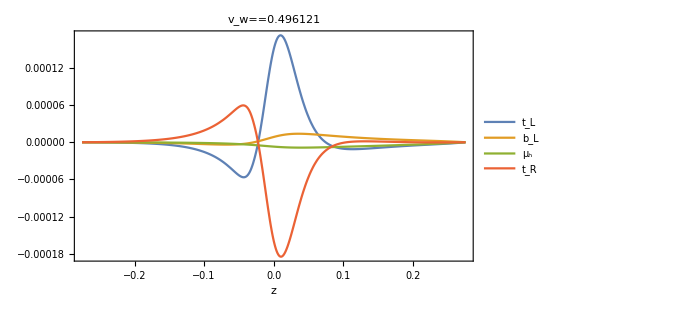
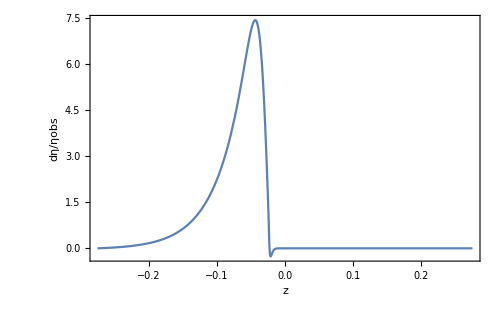
{-Graphics-,-Graphics-,0.454902}

```mathematica
MasterOutputVel[1,Lamlist[[1]],500]
```

```mathematica
BAUscale[i_]:=Module[{BAU,res,numpoints=100},

BAU[Λ_?NumericQ]:=BAU[Λ?NumericQ]=MasterOutputVel[i,Λ,numpoints][[3]];

If[BAU[100]<1,Print[Show[MasterOutputVel[i,100,numpoints][[1]]]];Print["Did not work!!, \n Λ_CP="];Return[99]];

Quiet[
res=Λ/.FindRoot[BAU[Λ]-1,{Λ,100,1000},AccuracyGoal->2,PrecisionGoal->2(*,EvaluationMonitor:>Print["Λ=",Λ," BAU=",BAU[Λ]]*)];
];

MasterPars[i];
Print[MasterOutputVel[i,res,numpoints][[1]]];
Print["Λ=",res];
Return[res]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Pars α=0.0187036 T_n=93.8922 v_w=0.659907 T_p=108.835 v_p=0.488539 h_0=204.479 L_h=0.0429076 s_l=117.2 s_h=4.83655 L_s=0.0429075 ds=0.497581

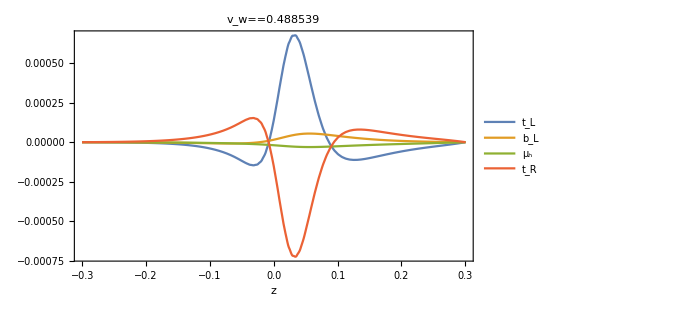

Λ=606.073

606.073

```mathematica
BAUscale[2]
```

```mathematica
BAULambda80=ParallelTable[Join[{vwlist[[i]],Tnlist[[i]],vplist[[i]],TpoverTnlist[[i]]Tnlist[[i]],alphalist[[i]]},{BAUscale[i]}],{i,1,Length[Tnlist]}];
Export["SCANS/BAU/BAU_5.csv",BAULambda80]
```

SCANS/BAU/BAU_5.csv

```mathematica
ComputeEta[i_]:=ComputeEta[i]=Module[{ii=i}, output=MasterOutputVel[ii,Lamlist[[ii]],100]; 
Print[output[[1]]];
Print["η=",output[[3]]];
Return[output[[3]]]]
```

```mathematica
ComputeEta[12]
```

0.0900786

```mathematica
etaExport=ParallelTable[ComputeEta[i],{i,1,Length[Lamlist]}];
```

Legended[-Graphics-, Placed[LineLegend[{Directive[FontColor -> GrayLevel[0], 
 
>       FontWeight -> Normal, FontSize -> 16, FontFamily -> Times, 
 
>       Opacity[1.], RGBColor[0.368417, 0.506779, 0.709798], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[FontColor -> GrayLevel[0], FontWeight -> Normal, 
 
>       FontSize -> 16, FontFamily -> Times, Opacity[1.], 
 
>       RGBColor[0.880722, 0.611041, 0.142051], AbsoluteThickness[1.6]], 
 
>      Directive[FontColor -> GrayLevel[0], FontWeight -> Normal, 
 
>       FontSize -> 16, FontFamily -> Times, Opacity[1.], 
 
>       RGBColor[0.560181, 0.691569, 0.194885], AbsoluteThickness[1.6]], 
 
>      Directive[FontColor -> GrayLevel[0], FontWeight -> Normal, 
 
>       FontSize -> 16, FontFamily -> Times, Opacity[1.], 
 
>       RGBColor[0.922526, 0.385626, 0.209179], AbsoluteThickness[1.6]]}, 
 
>     {t ,  b ,  μ , t }, LegendMarkers -> None, LabelStyle -> {}, 
        L    L    h   R
 
>     LegendLayout -> Column], After, Identity]]

η=0.454902

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

«5 more identical outputs»

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

η=0.00373404

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

η=0.0830521

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

η=0.059883

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

η=0.0719215

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

η=0.0305537

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

η=0.0402198

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

η=0.231728

η=0.200841

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

«2 more identical outputs»

NDSolve::berr: The scaled boundary value residual error of 147.433
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

η=0.00490176

NDSolve::berr: The scaled boundary value residual error of 3.15422
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::berr: The scaled boundary value residual error of 862552.
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NDSolve::berr: The scaled boundary value residual error of 55963.1
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

η=0.000320771

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

η=0.015435

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

η=1.02176

NDSolve::berr: The scaled boundary value residual error of 105293.
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

η=0.10033

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

15
NDSolve::berr: The scaled boundary value residual error of 1.74023 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

12
NDSolve::berr: The scaled boundary value residual error of 8.82366 10
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

NIntegrate::maxp: 
   The integral failed to converge after 50000
     integrand evaluations. NIntegrate obtained -660.69 and 21.5741
     for the integral and error estimates.

NIntegrate::maxp: 
   The integral failed to converge after 50000
     integrand evaluations. NIntegrate obtained -4.0222 and 0.126917
     for the integral and error estimates.

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

7
η=1.04026 10

η=54804.

NDSolve::bvluc: 
   The equations derived from the boundary conditions are numerically
    ill-conditioned. The boundary conditions may not be sufficient to uniquely
    define a solution. If a solution is computed, it may match the boundary
    conditions poorly.

NDSolve::berr: The scaled boundary value residual error of 171.345
     indicates that the boundary values are not satisfied to specified
     tolerances. Returning the best solution found.

Legended[-Graphics-, Placed[LineLegend[{Directive[Opacity[1.], 
 
>       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.880722, 0.611041, 0.142051], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.560181, 0.691569, 0.194885], 
 
>       AbsoluteThickness[1.6]], 
 
>      Directive[Opacity[1.], RGBColor[0.922526, 0.385626, 0.209179], 
 
>       AbsoluteThickness[1.6]]}, {t ,  b ,  μ , t }, LegendMarkers -> None, 
                                    L    L    h   R
 
>     LabelStyle -> {}, LegendLayout -> Column], After, Identity]]

η=0.000293132

## Yukawa mass full formula

```mathematica
ClearAll["Global`*"];
(*SetDirectory[NotebookDirectory[]];*)
```

```mathematica
SetOptions[{ParametricPlot,ListLinePlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot,ListContourPlot,LogPlot,Plot,RegionPlot,ContourPlot},Frame->True,BaseStyle->{FontColor->Black,FontWeight->"Normal",FontSize->16,FontFamily->"Times"},Axes->False,PlotLegends->Automatic,AspectRatio->1,ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->Full];
colours=ColorData[97,"ColorList"];
```

```mathematica
WP=MachinePrecision;
(*******************************************************************************************************************)
(**********************************************************************************************)
```

```mathematica
(*gtab=Import["standardmodel2018.txt","Table",HeaderLines->8][[;;;;20]];*)
gtab=Import["/Users/marcoantoniomerchandmedina/Documents/GitHub/Z_2breaking/satoshi_dof.dat","Table",HeaderLines->8][[;;;;20]];
gstar[T_]:=Interpolation[gtab[[All,{1,2}]]][T];
gsstar[T_]:=Interpolation[gtab[[All,{1,4}]]][T];
(*****************************************************************************************************)
(*****************************************************************************************************)
```

```mathematica
params3=Import["/Users/marcoantoniomerchandmedina/Documents/GitHub/Z_2breaking/SCANS/computeBAU.csv","Dataset","HeaderLines"->1];
Tnlist=params3[All,"Tnuc_0"]//Normal;
TpoverTnlist=params3[All,"Tp/TN"]//Normal;
vwlist=params3[All,"vw"]//Normal;
vplist=params3[All,"vp"]//Normal;
h0list=params3[All,"h0"]//Normal;
Lhlist=params3[All,"Lh"]//Normal;
Lslist=params3[All,"Ls"]//Normal;
dslist=params3[All,"ds"]//Normal;
shighlist=params3[All,"shigh"]//Normal;
slowlist=params3[All,"slow"]//Normal;
alphalist=params3[All,"alpha_max"]//Normal;
mslist=params3[All,"ms"]//Normal;Lamlist=params3[All,"Lam_CP"]//Normal;
```

```mathematica
MasterPars[i_]:=Print[ "Pars α=",alphalist[[i]],(*" β/H=",betalist[[i]],*)" T_n=",Tnlist[[i]]," v_w=",vwlist[[i]]," T_p=",Tnlist[[i]]*TpoverTnlist[[i]]," v_p=",vplist[[i]]," h_0=",h0list[[i]]," L_h=",Lhlist[[i]]," s_l=",slowlist[[i]]," s_h=",shighlist[[i]]," L_s=",Lslist[[i]]," ds=",dslist[[i]]," Λ_CP=",Lamlist[[i]]];
```

```mathematica
MasterPars[1]
```

Pars α=0.00106648 T_n=148.311 v_w=0.218217 T_p=148.349 v_p=0.217442 h_0=87.1634 L_h=0.14806 s_l=-69.1915 s_h=-61.1977 L_s=0.148059 ds=0.175901 Λ_CP=873.603

```mathematica
MasterFunction[Tn_,vw_,h0_,Lh_,sl_,sh_,Ls_,ds_,ΛCP_,Infty_,points_]:=MasterFunction[Tn,vw,h0,Lh,sl,sh,Ls,ds,ΛCP,Infty,points]=Module[{ηobs=8 10^-11,β=1/Tn,Γsph=10^-6 Tn,h,s,mt,Bond,Equation,sol,μtlsol,μtrsol,μblsol,μhsol,μBL,fsph,gdof,ηB,Plot1,Plot2,
ΓSS=4.9*10^-4 Tn,
Γy=4.2*10^-3 Tn,Dq=6/Tn(*quark diffusion constant*),
Dh=20/Tn(*higgs diffusion constant*),
inf=Infty Lh (*defines the region of interpolation/integration*)},
pw=√(w^2-x^2);(*Formula defined after A3*)
pz=1/(√(1-vw^2))(y pw-w vw);(*Formula defined after A3*)
Eb=1/(√(1-vw^2))(w-vw y pw);(*Formula defined after A3*)
Vs = √(pz^2)/√(pz^2+x^2);(*Formula  A4*)
Vh=Vs^2 1/(√(1-x^2/Eb^2));(*Formula  A5*);
ff=1/(Exp[β w]+1);(*Distribution funcion for fermion *)
fb=1/(Exp[β w]-1);(*Distribution funcion for boson *)
ff1=D[ff,w];(*Derivative of Distribution funcion for fermion *)
fb1=D[fb,w];(*Derivative of Distribution funcion for boson *)
ff2=D[ff1,w];(*Second Derivative of Distribution funcion for fermion *)
fb2=D[fb1,w];(*Second Derivative of Distribution funcion for boson *)
h[z_]:=h0/2(Tanh[z/Lh]+1);(**equation (50) LEFT MOVING WALL!!**)
(*s[z_]:=s0/2(1-Tanh[z/Ls-ds]);*)(**equation (50)**)
s[z_]:=(sl-sh)/2 Tanh[z/Ls-ds]+(sl+sh)/2;
mt[z_]:=0.99571/(√2) h[z] √(1+s[z]^2/ΛCP^2);(**equation (49)**)
θ[z_]:=ArcTan[s[z]/ΛCP];(**equation (49)**)
mb[z_]:=4.2*h[z]/h0 ;
mh[z_]:=125.3*h[z]/h0 ;
Γm[z_]:=mt[z]^2/(63 Tn);
mW[z_]:=0.65 h[z]/2 (*W boson mass*);
Γh[z_]:=mW[z]^2/(50Tn);
Xmax=Max[{mt[inf],mh[inf],mb[inf],mW[inf]}]+0.1(*Max value of x used for interpolating coefficient functions*);Kf0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2 NIntegrate[pw Eb ff/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for fermions*);
Kb0[xi_,vi_]:=(3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (43) for bosons*);
Kf0inter=Interpolation[Table[{x,Kf0[x,vw]},{x,0,Xmax,Xmax/10}]];
Kb0inter=Interpolation[Table[{x,Kb0[x,vw]},{x,0,Xmax,Xmax/10}]];
K0t[z_]:=Kf0inter[mt[z]];
K0b[z_]:=Kf0inter[mb[z]];
K0h[z_]:=Kb0inter[mh[z]];Df0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=0*);
Db0[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=0*);Df0inter=Interpolation[Table[{x,Df0[x,vw]},{x,0,Xmax,Xmax/10}]];
Db0inter=Interpolation[Table[{x,Db0[x,vw]},{x,0,Xmax,Xmax/10}]];
D0t[z_]:=Df0inter[mt[z]];
D0b[z_]:=Df0inter[mb[z]];
D0h[z_]:=Db0inter[mh[z]];Df1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=1*);
Db1[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[pw pz fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=1*);
Df1inter=Interpolation[Table[{x,Df1[x,vw]},{x,0,Xmax,Xmax/10}]];
Db1inter=Interpolation[Table[{x,Db1[x,vw]},{x,0,Xmax,Xmax/10}]];
D1t[z_]:=Df1inter[mt[z]];
D1b[z_]:=Df1inter[mb[z]];
D1h[z_]:=Db1inter[mh[z]];Df2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for fermions, l=2*);
Db2[xi_,vi_]:=(-3 √(1-vi^2))/π^2 β^2NIntegrate[(pw pz^2)/Eb fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1}](*Formula (26) for bosons, l=2*);Df2inter=Interpolation[Table[{x,Df2[x,vw]},{x,0,Xmax,Xmax/10}]];
Db2inter=Interpolation[Table[{x,Db2[x,vw]},{x,0,Xmax,Xmax/10}]];
D2t[z_]:=Df2inter[mt[z]];
D2b[z_]:=Df2inter[mb[z]];
D2h[z_]:=Db2inter[mh[z]];Qf1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[pw  ff2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞}](*Formula (27) for fermions, l=1*);
Qb1[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[pw  fb2/.{x->0,vvw->vi},{y,-1,1}],{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw  fb2/.{x->xi,vvw->vi},{y,-1,1},{w,xi,∞},WorkingPrecision->10]](*Formula (27) for bosons, l=1*);
Qf1inter=Interpolation[Table[{x,Qf1[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb1inter=Interpolation[Table[{x,Qb1[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1t[z_]:=Qf1inter[mt[z]];
Q1b[z_]:=Qf1inter[mb[z]];
Q1h[z_]:=Qb1inter[mh[z]];
Qf2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2NIntegrate[(pw pz)/Eb ff2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10](*Formula (27) for fermions, l=2*);
Qb2[xi_,vi_]:=(-3 √(1-vi^2))/(2 π^2)β^2If[xi==0,NIntegrate[Integrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{y,-1,1}],{w,xi,∞,xi},Method->PrincipalValue],NIntegrate[(pw pz)/Eb fb2/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (27) for bosons, l=2*);Qf2inter=Interpolation[Table[{x,Qf2[x,vw]},{x,0,Xmax,Xmax/10}]];
Qb2inter=Interpolation[Table[{x,Qb2[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2t[z_]:=Qf2inter[mt[z]];
Q2b[z_]:=Qf2inter[mb[z]];
Q2h[z_]:=Qb2inter[mh[z]];
Q1fo8integrand=FullSimplify[(Integrate[pw/pz Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh ff1/.{x->0,vw->vi},y]/.{y->-1})];Q1bo8integrand=FullSimplify[(Integrate[pw/pz Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh fb1/.{x->0,vw->vi},y]/.{y->-1})];Q1fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=1, helicity eigenstates*);
Q1bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q1bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=1, helicity eigenstates*);Q1fo8inter=Interpolation[Table[{x,Q1fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1bo8inter=Interpolation[Table[{x,Q1bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o8t[z_]:=Q1fo8inter[mt[z]];
Q1o8b[z_]:=Q1fo8inter[mb[z]];
Q1o8h[z_]:=Q1bo8inter[mh[z]];Q2fo8integrand=FullSimplify[(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh ff1/.{x->0,vvw->vi},y]/.{y->-1})];Q2bo8integrand=FullSimplify[(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb Vh fb1/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2fo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh ff1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for fermions, l=2, helicity eigenstates*);
Q2bo8[xi_,vi_]:=1/2(-3 √(1-vi^2))/π^2 β^2If[xi==0,NIntegrate[Q2bo8integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb Vh fb1/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (40) for bosons, l=2, helicity eigenstates*);Q2fo8inter=Interpolation[Table[{x,Q2fo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2bo8inter=Interpolation[Table[{x,Q2bo8[x,vw]},{x,0,Xmax,Xmax/10}]];
Q2o8t[z_]:=Q2fo8inter[mt[z]];
Q2o8b[z_]:=Q2fo8inter[mb[z]];
Q2o8h[z_]:=Q2bo8inter[mh[z]];
Q1fo9integrand=FullSimplify[(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q1fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q1fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/pz Vh/Eb (ff1/Eb-1/√(1-vw^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->10]](*Formula (41), l=1, helicity eigenstates*);Q1fo9nter=Interpolation[Table[{x,Q1fo9[x,vw]},{x,0,Xmax,Xmax/10}]];
Q1o9t[z_]:=Q1fo9nter[mt[z]];
Q1o9b[z_]:=Q1fo9nter[mb[z]];
Q2fo9integrand=FullSimplify[(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->1})-(Integrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->0,vvw->vi},y]/.{y->-1})];Q2fo9[xi_,vi_]:=(-3 √(1-vi^2))/(4 π^2)β^2If[xi==0,NIntegrate[Q2fo9integrand,{w,0,∞,0},Method->PrincipalValue],NIntegrate[pw/Eb^2 Vh (ff1/Eb-1/√(1-vi^2)ff2)/.{x->xi,vvw->vi},{w,xi,∞},{y,-1,1},WorkingPrecision->15]](*Formula (41) for fermions, l=2, helicity eigenstates*);Q2fo9inter=Interpolation[Table[{x,Q2fo9[x,vw]},{x,0,Xmax,Xmax/10}]];Q2o9t[z_]:=Q2fo9inter[mt[z]];
Q2o9b[z_]:=Q2fo9inter[mb[z]];
St1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q1o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q1o9t[z])/.{z->zz}];Sb1[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q1o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q1o9b[z])/.{z->zz}];St2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mt[z]^2 D[θ[z],z],z]Q2o8t[z]-D[(mt[z])^2,z] mt[z]^2 D[θ[z],z]Q2o9t[z])/.{z->zz}];Sb2[zz_]:=Evaluate[-vw/(√(1-vw^2))(D[mb[z]^2 D[θ[z],z],z]Q2o8b[z]-D[(mb[z])^2,z] mb[z]^2 D[θ[z],z]Q2o9b[z])/.{z->zz}];
Γhtot[z_]:=D2h[z]/(Dh D0h[z])(*W scattering rate. This was not provided in the paper and we took it directly from ref [47] 0605242*);Γttot[z_]:=D2t[z]/(Dq D0t[z]);
Γbtot[z_]:=D2b[z]/(Dq D0b[z]);
δCtL1[z_]:=β K0t[z] (Γy(μtl[z]-μtr[z]+μh[z])+Γm[z](μtl[z]-μtr[z])+Γhtot[z](μtl[z]-μbl[z])+ ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]))(*Formula (53), we divide by T to get dimensions right*);δCtL2[z_]:=(-Γttot[z]utl[z]-vw δCtL1[z]);
δCbL1[z_]:=β K0b[z](Γy(μbl[z]-μtr[z]+μh[z])+Γhtot[z](μbl[z]-μtl[z])+ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));δCbL2[z_]:=(-Γbtot[z]ubl[z]-vw δCbL1[z]);δCtR1[z_]:=β K0t[z](-Γy(μtl[z]+μbl[z]-2μtr[z]+2μh[z])-Γm[z](μtl[z]-μtr[z])-ΓSS ((1+9D0t[z])μtl[z]+(1+9D0b[z])μbl[z]-(1-9D0t[z])μtr[z]));
δCtR2[z_]:=(-Γttot[z]utr[z]-vw δCtR1[z]);
δCh1[z_]:=β K0h[z]( Γy (μtl[z]+μbl[z]-2μtr[z]+2μh[z])+Γh[z] μh[z]);
δCh2[z_]:=(-Γhtot[z]uh[z]-vw δCh1[z]);
{htl,htr,hbl}={-1,1,-1};TopLeft1={-D1t[z] μtl'[z]+utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q1t[z] μtl[z]-δCtL1[z]==htl St1[z]};TopLeft2={-D2t[z] μtl'[z]-vw utl'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtl[z]-δCtL2[z]== htl St2[z]};
BottomLeft1={-D1b[z] μbl'[z]+ubl'[z]+ D[(mb[z])^2,z] vw/(√(1-vw^2))Q1b[z] μbl[z]-δCbL1[z]==hbl Sb1[z]};BottomLeft2={-D2b[z] μbl'[z]-vw ubl'[z]+D[(mb[z])^2,z] vw/(√(1-vw^2)) Q2b[z] μbl[z]-δCbL2[z]==hbl Sb2[z]};TopRight1={-D1t[z] μtr'[z]+utr'[z]+ D[(mt[z])^2,z] vw/(√(1-vw^2))Q1t[z] μtr[z]-δCtR1[z]==htr St1[z]};TopRight2={-D2t[z] μtr'[z]-vw utr'[z]+D[(mt[z])^2,z] vw/(√(1-vw^2)) Q2t[z] μtr[z]-δCtR2[z]==htr St2[z]};Higgs1={-D1h[z] μh'[z]+uh'[z]+ D[(mh[z])^2,z] vw/(√(1-vw^2))Q1h[z] μh[z]-δCh1[z]==0};
Higgs2={-D2h[z] μh'[z]-vw uh'[z]+D[(mh[z])^2,z] vw/(√(1-vw^2)) Q2h[z] μh[z]-δCh2[z]==0};
Bond={ μtl[inf]==0,μtr[inf]==0,μbl[inf]==0,μh[inf]==0, μtl[-inf]==0,μtr[-inf]==0,μbl[-inf]==0,μh[-inf]==0};Equation=Join[TopLeft1,TopLeft2,TopRight1,TopRight2,BottomLeft1,BottomLeft2,Higgs1,Higgs2,Bond];sol=NDSolve[Equation,{μtl,μtr,μbl,μh, utl,utr,ubl,uh},{z,-inf,inf},Method->{"Shooting",Method->{"FixedStep",Method->"ExplicitEuler"}},StartingStepSize->2inf/points(*,Method->{"Shooting",Method->"StiffnessSwitching"},MaxStepSize->0.01*)];μtlsol[z_]:=μtl[z]/.sol[[1]][[1]];μtrsol[z_]:=μtr[z]/.sol[[1]][[2]];μblsol[z_]:=μbl[z]/.sol[[1]][[3]];μhsol[z_]:=μh[z]/.sol[[1]][[4]];μBL[z_]:=1/2(1+4D0t[z])μtlsol[z]+1/2(1+4D0b[z])μblsol[z]+2 D0t[z] μtrsol[z];
fsph[z_]:=Min[{1,2.5 Tn/Γsph Exp[-40 h[z]/Tn]}];
gdof=gstar[Tn](*106.75*);
ηB=405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2) NIntegrate[μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)],{z,-inf,inf},Method->"QuasiMonteCarlo",AccuracyGoal->2,PrecisionGoal->2];
Plot2=Plot[405 Γsph/(4π^2 vw gdof Tn)√(1-vw^2)μBL[z] fsph[z ]Exp[-45Γsph Abs[z]/(4 Abs[vw])(*√(1-vw^2)*)]/ηobs,{z,-inf,inf},FrameLabel->{"z","dη/ηobs"},PlotRange->All];
Plot1=Plot[{μtlsol[z] β,μblsol[z] β,μhsol[z] β,μtrsol[z]β},{z,-inf,inf},PlotRange->Full,PlotLegends->{"t_L"," b_L"," μ_h","t_R"},PlotLabel->Subscript[v, w]==-vw,FrameLabel->{"z",""},PlotRange->All];
(*Return[Abs[ηB/ηobs]];*)
Return[{Plot1,Plot2,Abs[ηB/ηobs]}];
];
```

```mathematica
MasterOutputVel[i_,Λcutoff_,Infty_,points_]:=MasterFunction[Tnlist[[i]]*TpoverTnlist[[i]],-vplist[[i]],h0list[[i]],Lhlist[[i]],slowlist[[i]],shighlist[[i]],Lslist[[i]],dslist[[i]],Λcutoff,Infty,points];
```

```mathematica
ComputeEta[i_,points_]:=ComputeEta[i,points]=Module[{ii=i,InfLh=10/Log[(Tnlist[[i]]*Lhlist[[i]])],Points=points}, output=MasterOutputVel[ii,Lamlist[[ii]],InfLh,Points]; 
Print[output[[1]]];
Print["η=",output[[3]]];
Return[output[[3]]]];
```

```mathematica
MasterPars[10]
```

Pars α=0.00177948 T_n=144.33 v_w=0.313977 T_p=144.47 v_p=0.311843 h_0=108.958 L_h=0.0970377 s_l=-66.1597 s_h=-51.2252 L_s=0.0970372 ds=0.00157198 Λ_CP=1014.15

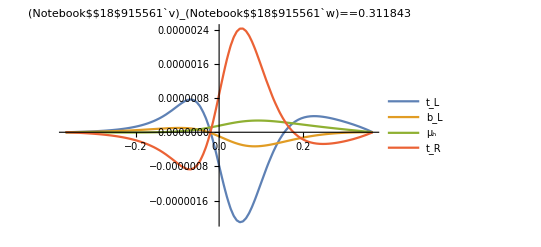

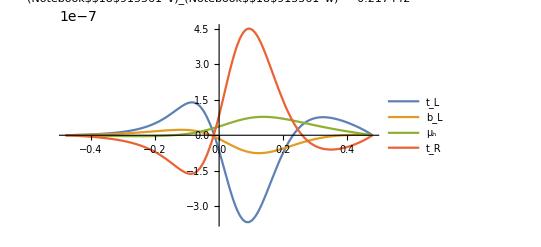

η=0.0212127

η=0.00456448

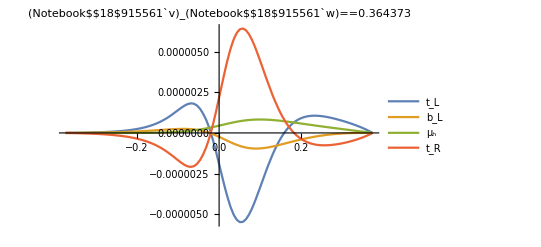

η=0.041061

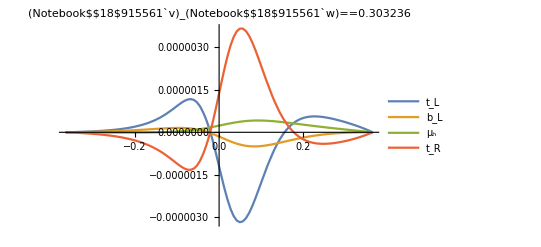

η=0.0315449

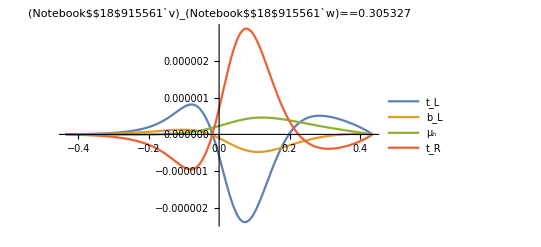

η=0.0246097

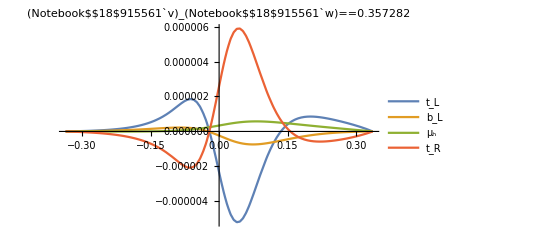

η=0.0400889

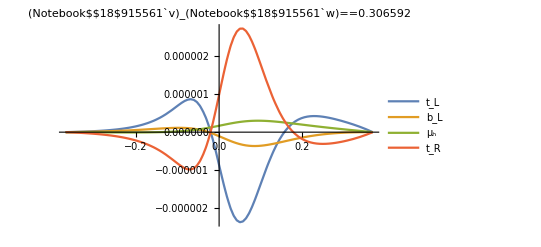

η=0.0251008

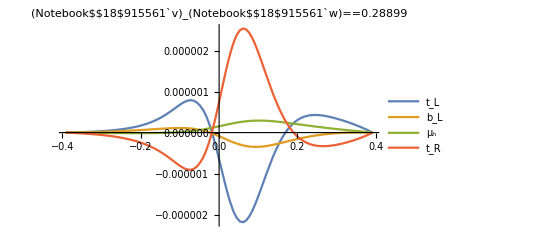

η=0.0293213

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

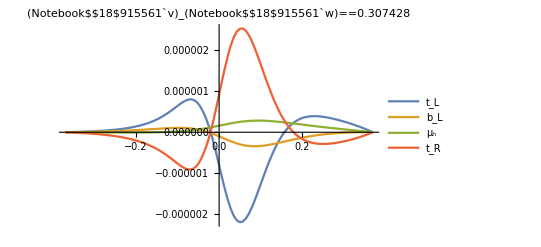

η=0.0229075

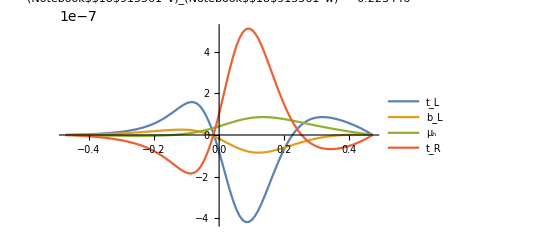

η=0.00489258

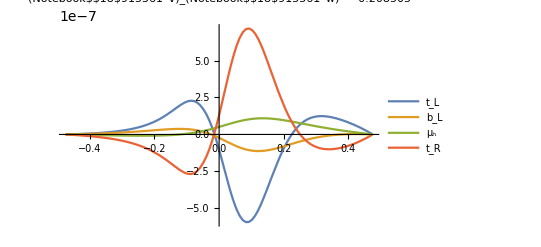

η=0.0133771

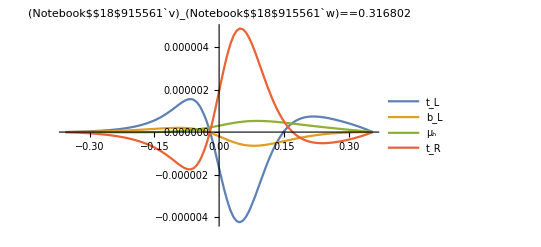

η=0.0400399

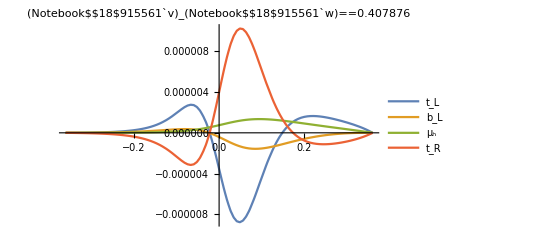

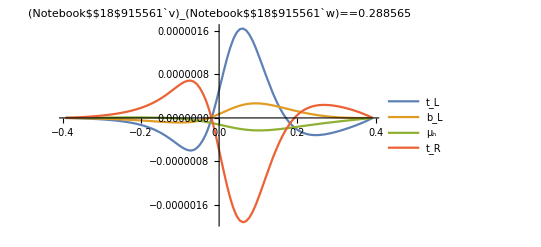

η=0.0469606

η=0.0212282

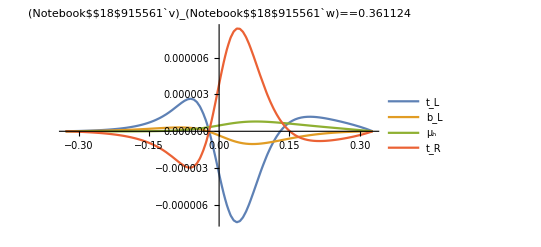

η=0.0550966

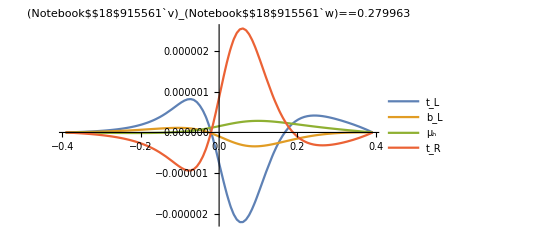

η=0.0306276

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

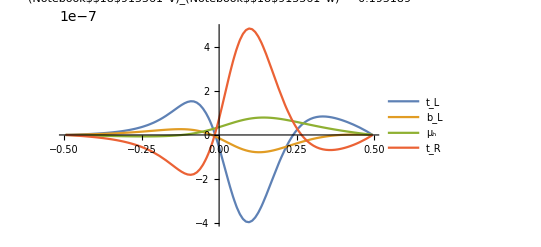

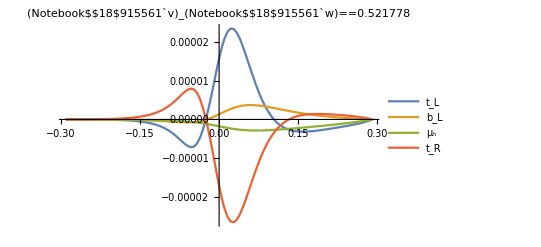

η=0.00976213

η=0.046893

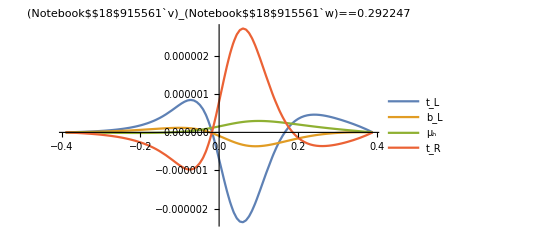

η=0.0313229

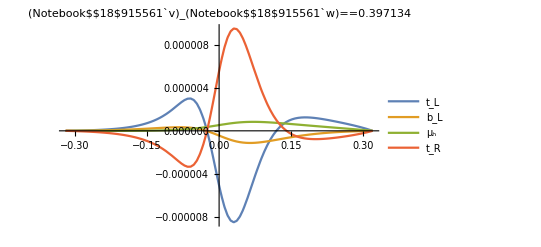

η=0.0517801

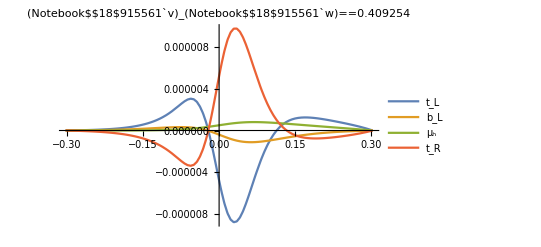

η=0.0488668

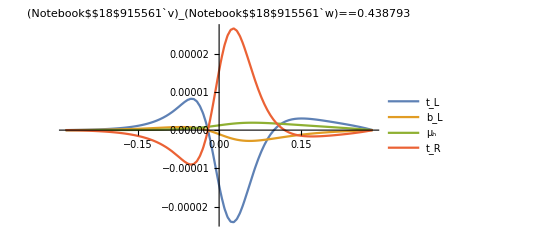

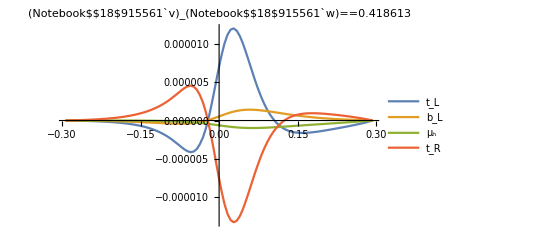

η=0.109125

η=0.0623726

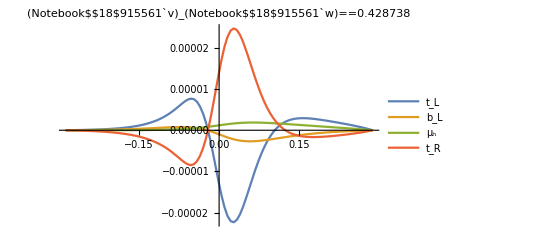

η=0.108812

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

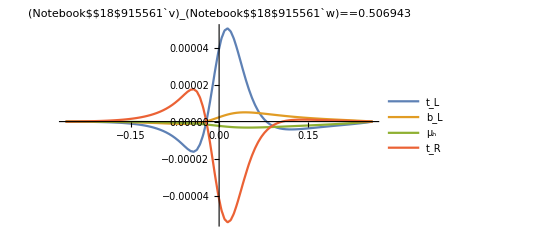

η=0.135164

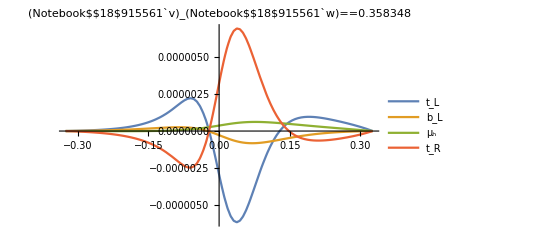

η=0.0476595

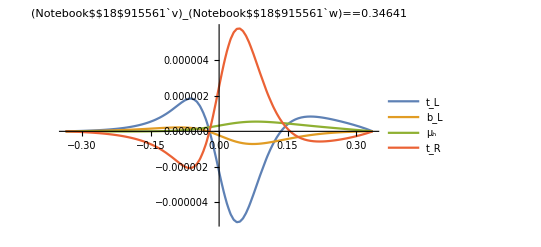

η=0.0425606

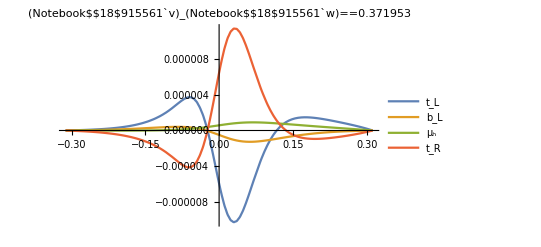

η=0.072055

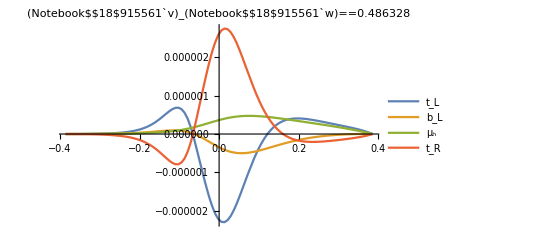

η=0.00116615

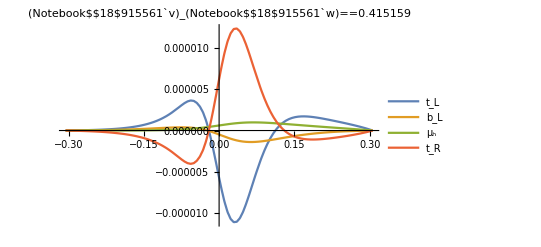

η=0.0591337

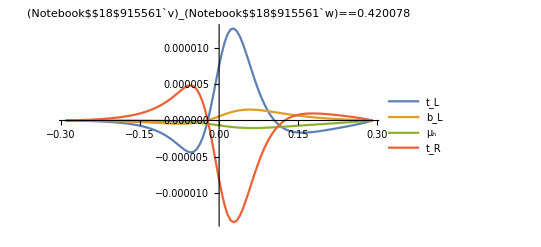

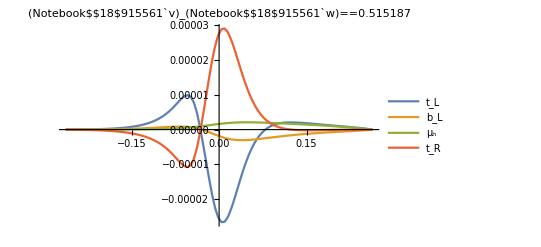

η=0.0652726

η=0.0638846

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

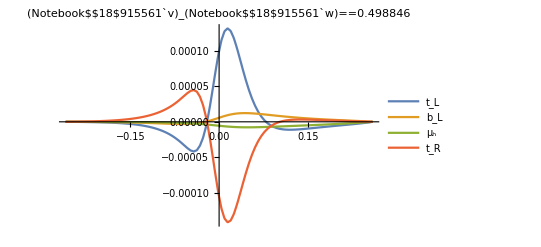

η=0.359008

{0.00456448,0.00489258,0.00976213,0.0246097,0.0133771,0.0315449,0.0469606,0.041061,0.0400399,0.0212127,0.0229075,0.0251008,0.0212282,0.0293213,0.0306276,0.0400889,0.0550966,0.046893,0.0425606,0.0313229,0.0476595,0.0517801,0.072055,0.0488668,0.00116615,0.108812,0.0652726,0.109125,0.0591337,0.0623726,0.0638846,0.135164,0.359008}

```mathematica
etaExport=ParallelTable[ComputeEta[i,100],{i,1,Length[Lamlist]}]
```

```mathematica
etaExport
```

{0.00456448,0.00489258,0.00976213,0.0246097,0.0133771,0.0315449,0.0469606,0.041061,0.0400399,0.0212127,0.0229075,0.0251008,0.0212282,0.0293213,0.0306276,0.0400889,0.0550966,0.046893,0.0425606,0.0313229,0.0476595,0.0517801,0.072055,0.0488668,0.00116615,0.108812,0.0652726,0.109125,0.0591337,0.0623726,0.0638846,0.135164,0.359008}

```mathematica
Export["/Users/marcoantoniomerchandmedina/Documents/GitHub/Z_2breaking/SCANS/BAU/BAU_top_fullmodel_3.csv",etaExport]
```

/Users/marcoantoniomerchandmedina/Documents/GitHub/Z_2breaking/SCANS/BAU/BAU_top_fullmodel_3.csv

```mathematica
Length[etaExport]
```

33